```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/sandrews/SSA/software/Smoldyn/trunk/examples/S7_surfaces/surfacediffuse

```mathematica
timestep=10
diffconst=10
binlow=0
binhigh=100
binwidth=0.5
```

10

10

0

100

0.5

```mathematica
bendpos=30
```

30

```mathematica
(* Everything below here should take care of itself *)
```

```mathematica
(* Define functions *)
```

```mathematica
gauss[x_,mu_,sigma_]:=1/(sigma*Sqrt[2*Pi])*Exp[-(x-mu)^2/(2*sigma^2)]
```

```mathematica
(* Load and look at data *)
```

```mathematica
simdata=Import["simple2cout.txt"];
```

```mathematica
simdata
```

10 5368 5452 5838 6094 6401 6830 6808 7253 7636 7925 8087 8557 8930 9036 9568 9547 9932 10411 10763 10678 11261 11070 11565 12029 11790 12309 12795 12748 12733 13014 13442 13531 13606 13598 14043 14169 13794 14175 14003 14052 14179 13886 14106 13683 13997 13942 13553 13724 13484 13407 13205 13164 12614 12735 12458 11928 12012 11638 11082 11181 10872 10864 10170 9894 9324 9552 9031 8882 8638 8205 8064 7598 7248 6775 6832 6383 6029 5884 5740 5292 5050 4678 4696 4373 3991 3983 3724 3540 3413 2939 2934 2714 2429 2420 2234 1913 1954 1746 1638 1824 1277 1415 1256 1183 1028 975 720 1003 741 787 474 753 479 524 514 244 457 249 234 226 257 264 241 232 265 0 263 0 218 0 0 222 0 0 0 255 245 0 0 0
10 0 0 0 231 260 0 0 0 259 0 0 234 0 226 0 209 246 236 211 240 262 236 245 527 235 478 481 490 745 465 731 711 950 722 1019 1001 1267 1217 1490 1254 1617 1737 1714 1858 1959 2217 2492 2385 2694 2867 2966 3458 3474 3583 4041 3977 4425 4663 4641 5064

```mathematica
simdata2=StringReplace[simdata," "->","]
```

10,5368,5452,5838,6094,6401,6830,6808,7253,7636,7925,8087,8557,8930,9036,9568,9547,9932,10411,10763,10678,11261,11070,11565,12029,11790,12309,12795,12748,12733,13014,13442,13531,13606,13598,14043,14169,13794,14175,14003,14052,14179,13886,14106,13683,13997,13942,13553,13724,13484,13407,13205,13164,12614,12735,12458,11928,12012,11638,11082,11181,10872,10864,10170,9894,9324,9552,9031,8882,8638,8205,8064,7598,7248,6775,6832,6383,6029,5884,5740,5292,5050,4678,4696,4373,3991,3983,3724,3540,3413,2939,2934,2714,2429,2420,2234,1913,1954,1746,1638,1824,1277,1415,1256,1183,1028,975,720,1003,741,787,474,753,479,524,514,244,457,249,234,226,257,264,241,232,265,0,263,0,218,0,0,222,0,0,0,255,245,0,0,0
10,0,0,0,231,260,0,0,0,259,0,0,234,0,226,0,209,246,236,211,240,262,236,245,527,235,478,481,490,745,465,731,711,950,722,1019,1001,1267,1217,1490,1254,1617,1737,1714,1858,1959,2217,2492,2385,2694,2867,2966,3458,3474,3583,4041,3977,4425,4663,4641,5064

```mathematica
simdata3=ImportString[simdata2,"CSV"]
```

{{10,5368,5452,5838,6094,6401,6830,6808,7253,7636,7925,8087,8557,8930,9036,9568,9547,9932,10411,10763,10678,11261,11070,11565,12029,11790,12309,12795,12748,12733,13014,13442,13531,13606,13598,14043,14169,13794,14175,14003,14052,14179,13886,14106,13683,13997,13942,13553,13724,13484,13407,13205,13164,12614,12735,12458,11928,12012,11638,11082,11181,10872,10864,10170,9894,9324,9552,9031,8882,8638,8205,8064,7598,7248,6775,6832,6383,6029,5884,5740,5292,5050,4678,4696,4373,3991,3983,3724,3540,3413,2939,2934,2714,2429,2420,2234,1913,1954,1746,1638,1824,1277,1415,1256,1183,1028,975,720,1003,741,787,474,753,479,524,514,244,457,249,234,226,257,264,241,232,265,0,263,0,218,0,0,222,0,0,0,255,245,0,0,0},{10,0,0,0,231,260,0,0,0,259,0,0,234,0,226,0,209,246,236,211,240,262,236,245,527,235,478,481,490,745,465,731,711,950,722,1019,1001,1267,1217,1490,1254,1617,1737,1714,1858,1959,2217,2492,2385,2694,2867,2966,3458,3474,3583,4041,3977,4425,4663,4641,5064}}

```mathematica
simdata4=Join[Drop[simdata3[[2]],1],Drop[simdata3[[1]],1]]
```

{0,0,0,231,260,0,0,0,259,0,0,234,0,226,0,209,246,236,211,240,262,236,245,527,235,478,481,490,745,465,731,711,950,722,1019,1001,1267,1217,1490,1254,1617,1737,1714,1858,1959,2217,2492,2385,2694,2867,2966,3458,3474,3583,4041,3977,4425,4663,4641,5064,5368,5452,5838,6094,6401,6830,6808,7253,7636,7925,8087,8557,8930,9036,9568,9547,9932,10411,10763,10678,11261,11070,11565,12029,11790,12309,12795,12748,12733,13014,13442,13531,13606,13598,14043,14169,13794,14175,14003,14052,14179,13886,14106,13683,13997,13942,13553,13724,13484,13407,13205,13164,12614,12735,12458,11928,12012,11638,11082,11181,10872,10864,10170,9894,9324,9552,9031,8882,8638,8205,8064,7598,7248,6775,6832,6383,6029,5884,5740,5292,5050,4678,4696,4373,3991,3983,3724,3540,3413,2939,2934,2714,2429,2420,2234,1913,1954,1746,1638,1824,1277,1415,1256,1183,1028,975,720,1003,741,787,474,753,479,524,514,244,457,249,234,226,257,264,241,232,265,0,263,0,218,0,0,222,0,0,0,255,245,0,0,0}

```mathematica
Length[simdata4]
```

200

```mathematica
nmolec=Total[simdata4]
```

1000000

```mathematica
xvector=Table[i,{i,binlow+binwidth/2,binhigh-binwidth/2,binwidth}];
```

```mathematica
simdata5=Transpose[{xvector,simdata4}];
```

```mathematica
sigma=Sqrt[2*diffconst*timestep]
```

10 √2

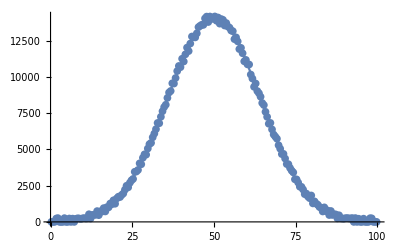

```mathematica
Show[{ListPlot[simdata5],Plot[nmolec*binwidth*gauss[x,50,sigma],{x,binlow,binhigh},PlotRange->All]},PlotRange->All]
```

```mathematica
residuals=Table[simdata4[[i]]-nmolec*binwidth*gauss[xvector[[i]],50,sigma],{i,1,Length[simdata4]}];
```

```mathematica
residuals2=Transpose[{xvector,residuals}];
```

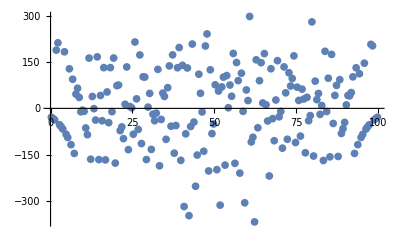

```mathematica
ListPlot[residuals2,PlotRange->All]
```

```mathematica
Min[residuals]
```

-368.522

```mathematica
Position[residuals,Min[residuals]]
```

{{125}}

```mathematica
xvector[[First[First[Position[residuals,Min[residuals]]]]]]
```

62.25